```mathematica
Solve[(k+α-1)/θ-(99+β-k)/(1-θ)==0,θ]
```

{{θ→(-1+k+α)/(98+α+β)}}

```mathematica
mle=FullSimplify[Sum[Binomial[100,k](θ-k/100)^2 θ^k(1-θ)^(100-k),{k,0,100}]]
```

-1/100 (-1+θ) θ

```mathematica
map1=FullSimplify[Sum[Binomial[100,k](θ-(k+5)/106)^2 θ^k(1-θ)^(100-k),{k,0,100}]]
```

(25+8 (5-8 θ) θ)/11236

```mathematica
map2=FullSimplify[Sum[Binomial[100,k](θ-(k+1)/106)^2 θ^k(1-θ)^(100-k),{k,0,100}]]
```

(1+8 (11-8 θ) θ)/11236

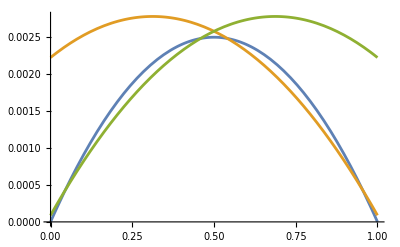

```mathematica
Plot[{mle,map1,map2},{θ,0,1}]
```